```mathematica
f={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),Nt1+Nt2==N};
f//TableForm
```

(1-τ)/(Nt1-A1 τ)==(1-τ)/(Nt2-A2 τ)
Nt1+Nt2==N

```mathematica
res=Solve[f,{Nt1,Nt2}]
```

{{Nt1→N/2+(A1 τ)/2-(A2 τ)/2,Nt2→N/2-(A1 τ)/2+(A2 τ)/2}}

```mathematica
Evaluate[res[[1,{1,2},2]]/.N->2]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

```mathematica
manu[A1_,A2_,τ_]:=Evaluate[res[[1,{1,2},2]]/.N->2]
```

```mathematica
Manipulate[ListLinePlot[Table[manu[A1,A2,t],{t,0,1,0.02}]ᵀ,PlotRange->{0,2},PlotLegends->{"A1","A2"}],{{A1,0.5},0,1},{A2,0,1},SaveDefinitions->True]
```

the result for simulate mono test.

```mathematica
Manipulate[ListLinePlot[
(Table[manu[t,a2,0.75],{t,0,1,0.02}]~Join~Table[manu[t,a2,0.75],{t,1,0,-0.02}])ᵀ~Join~{Range[0,1,0.02]~Join~Range[1,0,-0.02]},
PlotLabel->"mono test",PlotRange->{0,1.5},PlotLegends->{"total","free","used"}
],{{a2,0.5},0,1}]
```

the result for simulate random test.

```mathematica
r=RandomReal[1,50];
Manipulate[ListPlot[
manu[#,a2,0.75]&/@rᵀ~Join~{r},Filling->Axis,PlotRange->{0,1.5},PlotLegends->{"total","free","used"}
],{{a2,0.5},0,1},SaveDefinitions->True]
```

```mathematica
t={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt3-τ A3),Nt1+Nt2+Nt3==n};
```

```mathematica
t=Solve[t,{Nt1,Nt2,Nt3}];
```

```mathematica
manu3[A1_,A2_,A3_,τ_]:=Evaluate[t[[1,All,2]]/.n->3]
```

```mathematica
Manipulate[ListLinePlot[Table[manu3[A1,A2,A3,τ],{τ,0,1,0.02}]ᵀ,
PlotRange->{0,2},PlotLegends->{"A1","A2","A3"}
],{{A1,0.75},0,1},{{A2,0.5},0,1},{A3,0,1},SaveDefinitions->True]
```

#### the research about τ range

为了研究τ的范围.现在我们来观察下面一个事实.
1.在总内存能够满足分配的时候.需要分配的量大于等于申请的量也就是N_ti>=A_i.
   否则.会得出明明还有富余但是给你分配的反而无法满足需求的不可理解的情况.
所以列出方程{Nt1>=A1,Nt2>=A2,A1+A2<=N}最后根据τ画出来解区域.

```mathematica
Manipulate[RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2,{A1,0,2},{A2,0,2}],{{τ,0.75},0,2}]
```

为了分析.我们取出一些片段来分析.

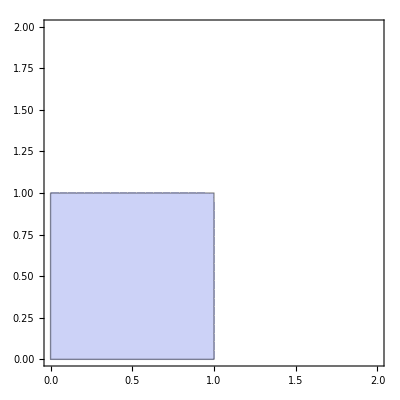

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->0,{A1,0,2},{A2,0,2}]
```

这个是τ等于0的时候的结果.可以看到.其中满足解的范围非常小.要求A1,A2<=1.也就是小于等于各自的初始内存.不能超过它.不然解就会违反条件1.
这个是非常的不合理的.
下面再看一下τ=0.75的情况

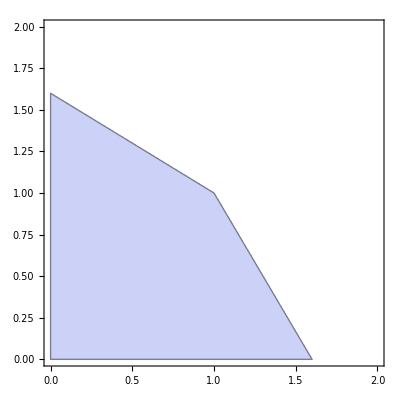

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->0.75,{A1,0,2},{A2,0,2}]
```

由此图可以看出.解区域的面积已经大于了τ=0的情况了.但是.明显的.还有一些问题.例如.1.5,0.5这个组合就无法满足解.也就是说.在τ=0.75的时候不能够提出一台虚拟机申请的内存是另外一台的3倍.
否则解就会异常.准确的来说.解出来的结果是manu[1.5,0.5,0.75]={1.375, 0.625},申请1.5却只能得到1.35.
下面再来看τ=1的情况.

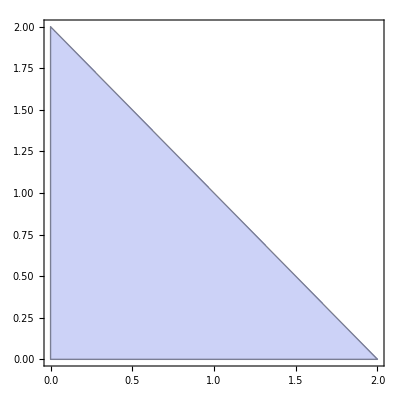

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->1,{A1,0,2},{A2,0,2}]
```

这个时候.解面积最大.在所有可以满足的情况下.都能够得到合理的解.
所以τ应该为1.

造成这种现象的原因是.整个解可以看作是N/n+Δ(A_i).所以第1项的N/n决定了解的性质.上下偏离的常数范围.

求反驳.

#### the research about τ value.

既然τ是线性变化的.所以在τ表达了一种变化范围的思想.当τ为0时.没有变化.当τ为1.时变化程度最剧烈.
所以可以求得基于τ的最大值和最小值.它们之间就是整个可变范围.

```mathematica
manu[A1,A2,τ]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

```mathematica
manu3[A1,A2,A3,tau]//Expand
```

{1+(2 A1 tau)/3-(A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3+(2 A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3-(A2 tau)/3+(2 A3 tau)/3}

当A1取最大,A2取最小时.就可以得到最大值,最小值集合了.再考虑一般解的情况.可以得出
一台虚拟机占用全部内存,其他虚拟机都为0时候就是范围集合.

```mathematica
range[τ_,n_]:={1+(n-1) τ,1-τ }
```

画出图像来

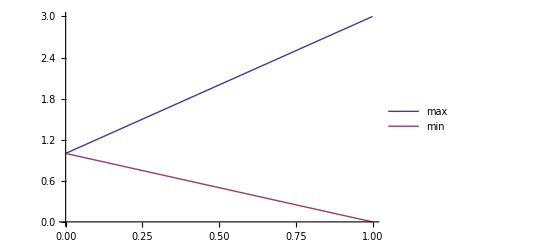

```mathematica
Plot[Evaluate[range[τ,3]],{τ,0,1},PlotLegends->{"max","min"}]
```

其中.非常明显的是,增加虚拟机的台数.只能增加最大值范围.也就是增加上界范围.但是下界范围却和虚拟机台数无关.

现在考虑τ=1的情况,会发现一个比较重要的事实.就是最小值为0.也就是说.可能会有虚拟机完全得不到内存.
在数学意义上.申请内存为0是完全可能的.这个时候理应该给它分配0.但是.事实上.一个运行操作系统的虚拟机不能够分配
0内存.这个和SWAP分区无关.
操作系统运行需要一个最小内存.来存放核心相关的内容.
也就是说要保证一台虚拟机的运行.不能够只是给他分配0内存.然后希望它把所有的运行需要的内存丢到
SWAP分区中.首先不考虑这样带来的巨大的性能损失.重要的是这个是完全不被允许的.
另外一方面.当不断的给一个运行的虚拟机减少分配的总内存的时候.当小于运行最小内存时.系统就会崩溃.造成KernelPanic.
所以虽然在数学意义上τ=1是具有全域可解的很好的性能.但是在这种情况下.会导致过度分配.导致分配0内存.所以需要一个
约束条件来限定它.也就是受保护的最小运行需要内存.作为τ的上界.
其计算公式为τ_up=1-系统最小内存/初始分配内存.因为在上面的计算中.为了简化表达.用1代表每台虚拟机初始分配内存.所以可用的总内存N=n*1.
为了换算成实际内存的MB单位.需要乘以初始内存(一般512~1024M).

```mathematica
tauUp[min_,cur_]:=1-min/cur
```

一般一个系统的最小运行内存和系统有关.运行X的Linux系统典型内存是512MB.现在很多系统要求最小1024MB.
不运行X的Linux服务器系统典型内存是192MB.一般可以分配256MB.
所以可以画出图像来:

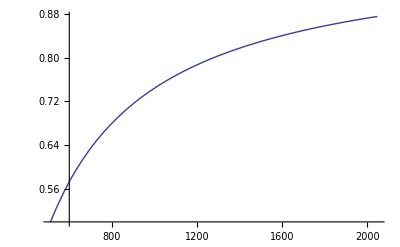

```mathematica
Plot[tauUp[256,m],{m,512,2048}]
```

在典型的初始内存1024MB,最小内存256MB的情况下.τ的上界即为0.75.

总结:通过设置τ为0.75.可以保证在具有尽可能大的可行解域范围的情况下.保护分配的最小内存.从而使得虚拟机能够正常运行.

bug:虽然tau为0.75的时候具有保护策略.但是这个是建立在某一台虚拟机提出申请0内存的情况下.
一般虚拟机正常运行之后,就不可能提出0内存.至少都是最小运行内存.所以提出0这一个条件是永远不可能满足的.
如果真要利用它.可能需要提出保护的最小可用内存.也就是让free memory不能低于某一个值.不过就算低于某一个值.也只是会加剧利用SWAP分区